```mathematica
(* There is a bug in the KnotTheory package, and this line should be added in somewhere: *)
```

```mathematica
MatrixWrapper/:MatrixWrapper[n_,N_].MatrixWrapper[k_,{}]:=MatrixWrapper[k,Table[Table[0,{k}],{Length[N]}]]
```

```mathematica
b=BR[2,Table[1,{3}]]
```

BR[2,{1,1,1}]

```mathematica
AllBigradings[b]
```

{{0,1},{0,3},{0,5},{1,3},{1,5},{2,3},{2,5},{2,7},{3,3},{3,5},{3,7},{3,9}}

```mathematica
DifferentialAsMatrix[b,0,3]
```

MatrixWrapper[2,{{1,1},{1,1},{1,1}}]

```mathematica
DD[b_]:=Table[(Transpose[DifferentialAsMatrix[b,t[[1]],t[[2]]]].DifferentialAsMatrix[b,t[[1]],t[[2]]]+DifferentialAsMatrix[b,t[[1]]-1,t[[2]]].Transpose[DifferentialAsMatrix[b,t[[1]]-1,t[[2]]]])[[2]],{t,AllBigradings[b]}]
```

```mathematica
Union[Flatten[Eigenvalues/@DD[b]]]
```

{0,1,2,3,4,5,6}

```mathematica
Union[Flatten[Eigenvalues/@N[DD[b]]]]
```

{-2.17696×10^-16,0.,1.,1.,2.,2.,2.,2.,3.,3.,4.,5.,5.,6.,6.}

```mathematica
gap[b_]:=With[{ev=Union[Flatten[Chop[Eigenvalues/@N[DD[b]]]]]},Min[Complement[ev,{0}]]/Max[ev]]
```

```mathematica
gap[b]
```

0.166667

```mathematica
Do[Print[gap[BR[2,Table[1,{k}]]]//AbsoluteTiming],{k,3,20}]
```

{0.002242,0.166667}

{0.03606,0.0784648}

{0.143711,0.0381966}

{0.865459,0.0271919}

{4.8049,0.0141473}

{26.8007,0.0126898}

{232.564,0.00670082}

$Aborted

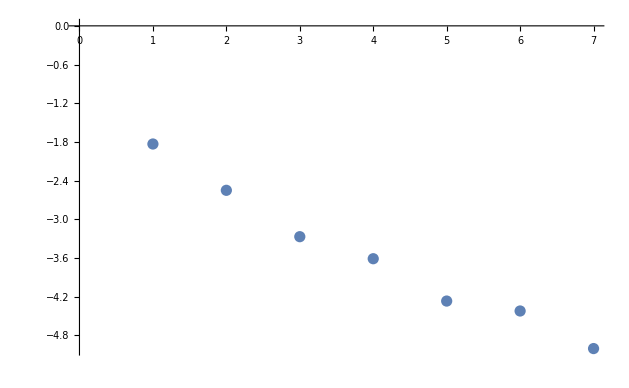

```mathematica
ListPlot[Log[{0.16,0.078,0.038,0.027,0.014,0.012,0.0067}]]
```